```mathematica
acc=10^-18;
```

```mathematica
sig[w_,NA_,V_]=( (w NA π^3)/V^2)^(-1/6);
```

```mathematica
rcut[a_,sig_]=(-Log[a] sig^2)^(1/2);
```

```mathematica
gcut[a_,sig_]=2/sig(-Log[a])^(1/2);
```

```mathematica
Quit[]
```

```mathematica
w=0.0123;
NA=10;
Vol=50;
```

```mathematica
sig[w,NA,Vol]
```

2.94734

```mathematica
rcut[acc,sig[we,Na,50]]
```

(2^(1/3) 5^(2/3) √Log[1000000000000000000])/(√π (Na we)^(1/6))

```mathematica
gcut[acc,sig[we,Na,50]]
```

(2/5)^(2/3) (Na we)^(1/6) √(π Log[1000000000000000000])

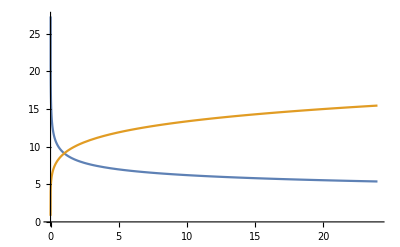

```mathematica
Plot[{(2^(1/6) √((5 Log[1000000000000000000])/π))/we^(1/6),(2^(5/6) we^(1/6) √(π Log[1000000000000000000]))/(√5)},{we,0,24}]
```

```mathematica
Manipulate[Plot[{(2^(1/3) 5^(2/3) √Log[1000000000000000000])/(√π (Na we)^(1/6)),(2/5)^(2/3) (Na we)^(1/6) √(π Log[1000000000000000000])},{we,0,60},PlotRange->{{0,40},{0,20}}],{Na,2,40}]
```